Simulation of stochastic process with only birth process

```mathematica
col1 = ColorData[97][1]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
col2 = ColorData[97][2]
```

RGBColor[0.880722, 0.611041, 0.142051]

```mathematica
RGBColor[col1]
```

```mathematica
RGBColor[HexToColor["#E75B6"]]
RGBColor[col2]
```

RGBColor[HexToColor[#E75B6]]

RGBColor[0.880722, 0.611041, 0.142051]

```mathematica
Clear[sim]
sim[λ_,intS_]:=sim[λ,intS]=Block[{out,Δt},out={{0,1}};
Δt=RandomVariate[ExponentialDistribution[λ out[[-1,2]]]];
While[out[[-1,1]]+Δt<1,
AppendTo[out,out[[-1]]+{Δt,1}];
Δt=RandomVariate[ExponentialDistribution[λ out[[-1,2]]]];
];
AppendTo[out,{1,out[[-1,2]]}];
out
]
```

```mathematica
sim[2,1]
```

{{0,1},{0.142216,2},{0.241299,3},{0.385083,4},{0.585059,5},{0.632711,6},{0.864207,7},{0.909091,8},{0.988682,9},{1,9}}

### Realized growth rate

```mathematica
rEff[λ_,intS_]:=Log[sim[λ,intS][[-1,2]]]//N
```

```mathematica
rEff[2.0,1]
```

1.60944

```mathematica
Clear[EstCIλ]
```

calculating confidence interval of growth rate

```mathematica
EstCIλ[λtrue_]:=EstCIλ[λtrue]=Block[{temp,min,max},
temp=Table[rEff[λtrue,intS],{intS,1,3000}];
min=Min[temp];max=Max[temp];
(*{Min[temp],Max[temp]}*)
temp=SmoothKernelDistribution[temp];
{temp,min,max}
]
```

```mathematica
tempInt[λtrue_]:=Interpolation[Table[{CDF[EstCIλ[λtrue][[1]],x],x},{x,EstCIλ[λtrue][[2]],EstCIλ[λtrue][[3]],(EstCIλ[λtrue][[3]]-EstCIλ[λtrue][[2]])/100}]]
```

```mathematica
EstCIλ2[λtrue_]:={tempInt[λtrue][0.025],tempInt[λtrue][0.975]}
```

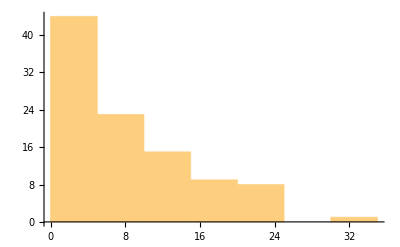

```mathematica
Table[sim[2,j][[-1,2]],{j,100}]//Histogram
```

```mathematica
xVec[λ_,intS_]:=xVec[λ,intS]=1-sim[λ,intS][[2;;,1]]
```

```mathematica
xVec[2.,2]
```

{0.547495,0.484676,0.366569,0.0817417,0}

### Phylogenetic Likelihood

```mathematica
ϕArg[λ_,τ_]:=-λ τ
```

```mathematica
Clear[ℓP]
ℓP[λin_,λtrue_,intS_]:=Block[{out},
out=Join[{ϕArg[λin,1]},Map[Log[λin]+ ϕArg[λin,#]&,xVec[λtrue,intS]]];
out//Total]
```

```mathematica
Clear[ℓPTab]
ℓPTab[λtrue_,intS_]:=ℓPTab[λtrue,intS]=Table[{λin,ℓP[λin,λtrue,intS]},{λin,λtrue/2,2λtrue,0.1}]
```

```mathematica
MPE[λtrue_,intS_]:=Sort[ℓPTab[λtrue,intS],#1[[2]]>#2[[2]]&][[1]]
```

```mathematica
Clear[CI]
CI[λtrue_,intS_]:=CI[λtrue,intS]=Select[ℓPTab[λtrue,intS],#[[2]]>MPE[λtrue,intS][[2]]-2&]
CILen[λtrue_,intS_]:=Max[CI[λtrue,intS][[;;,1]]]-Min[CI[λtrue,intS][[;;,1]]]
```

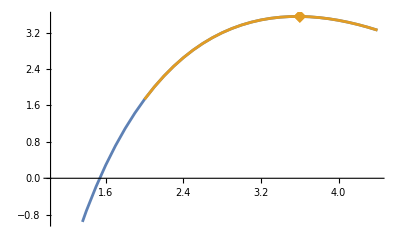

```mathematica
ListPlot[{ℓPTab[2.2,3],CI[2.2,3],{MPE[2.2,3]}},Joined->{True,True,False},PlotStyle->{col1,col2,col2},PlotMarkers->{None,None,{Automatic,13}}]
```

```mathematica
EstCIλ[5]
```

{DataDistribution[…],0.,7.29166}

```mathematica
EstCIλ2[5.0]
```

{1.44224,6.37237}

```mathematica
leg1=PointLegend[{col1,col2,Red},{"Case","Phylo","Truth"},LegendMarkerSize->8]
```

```mathematica
plot1[λTrue_,nSim_]:=Show[
(*True*)
ListLinePlot[{{λTrue,0},{λTrue,nSim+1}},PlotStyle->Red],
ListLinePlot[{{EstCIλ2[λTrue][[1]],nSim+1},{EstCIλ2[λTrue][[2]],nSim+1}},PlotStyle->Red],
(*Case*)
ListPlot[Table[{rEff[λTrue,intS],intS},{intS,1,nSim}],PlotStyle->col1],
(*Phylogeny*)
ListPlot[Table[{MPE[λTrue,intS][[1]],intS},{intS,1,nSim}],PlotStyle->col2],
ListLinePlot[Table[Map[{#,intS}&,CI[λTrue,intS][[;;,1]]],{intS,1,nSim}],PlotStyle->Directive[col2,Opacity[0.3]]],Epilog->Inset[leg1,Scaled[{0.9,0.5}]],Frame->True,Axes->False,FrameLabel->{"","Iterations"}]
```

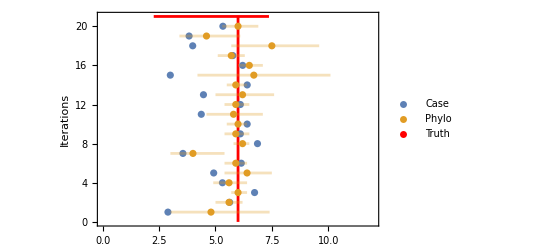

```mathematica
plot1[6,20]
```

```mathematica
leg1b=PointLegend[{col1,col2},{"Case","Phylo"},LegendMarkerSize->8,LabelStyle->Directive[FontSize->10,Bold]]
```

```mathematica
plot1b[λTrue_,nSim_]:=Show[
(*True*)
ListLinePlot[{{1,0},{1,nSim+1}},PlotStyle->Red],
ListLinePlot[{{(EstCIλ2[λTrue][[1]])/λTrue,nSim+1},{(EstCIλ2[λTrue][[2]])/λTrue,nSim+1}},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Truth"},LabelStyle->{FontSize->10,Bold}],Scaled[{0.12,0.32}]]],
(*Case*)
ListPlot[Table[{rEff[λTrue,intS]/λTrue,intS},{intS,1,nSim}],PlotStyle->col1],
(*Phylogeny*)
ListPlot[Table[{(MPE[λTrue,intS][[1]])/λTrue,intS},{intS,1,nSim}],PlotStyle->col2],
ListLinePlot[Table[Map[{#,intS}&,(CI[λTrue,intS][[;;,1]])/λTrue],{intS,1,nSim}],PlotStyle->Directive[col2,Opacity[0.3]]],Epilog->Inset[leg1b,Scaled[{0.1,0.5}]],Frame->True,Axes->False,FrameLabel->{{Style["Iterations",Bold,FontSize->12],None},{Style["/",Bold,FontSize->14],None}},PlotLabel->Style["λ: " <> IntegerString[Round[λTrue]],FontSize->14,Bold]
]
```

InterpolatingFunction::dmval: Input value {0.025} lies outside the range of data in the interpolating function. Extrapolation will be used.

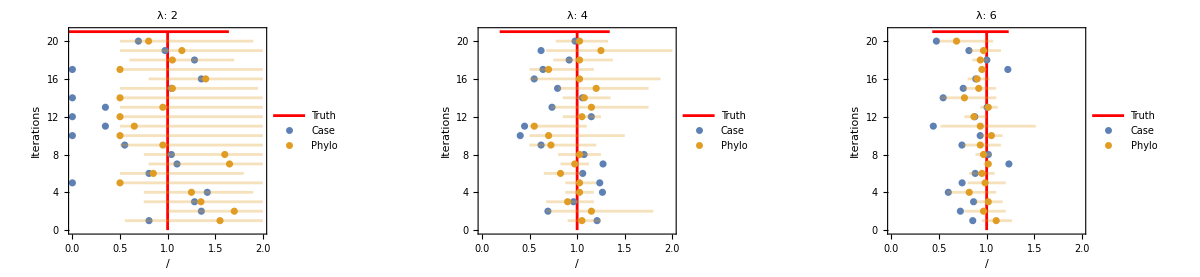

```mathematica
GraphicsRow[{plot1b[2.0,20],plot1b[4.0,20],plot1b[6.0,20]},ImageSize->Full]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/scatterYule.png",%,ImageRe]
```

Export::inselem: There are insufficient elements to export to PNG format.

$Failed

```mathematica
plot1b[λTrue_,nSim_]:=Show[
(*True*)
ListLinePlot[{{1,0},{1,nSim+1}},PlotStyle->Red],
ListLinePlot[{{(EstCIλ2[λTrue][[1]])/λTrue,nSim+1},{(EstCIλ2[λTrue][[2]])/λTrue,nSim+1}},PlotStyle->Red,PlotLegends->Placed[LineLegend[{"Truth"},LabelStyle->{FontSize->10,Bold}],Scaled[{0.12,0.32}]]],
(*Case*)
ListPlot[Table[{rEff[λTrue,intS]/λTrue,intS},{intS,1,nSim}],PlotStyle->col1],
(*Phylogeny*)
ListPlot[Table[{(MPE[λTrue,intS][[1]])/λTrue,intS},{intS,1,nSim}],PlotStyle->col2],
ListLinePlot[Table[Map[{#,intS}&,(CI[λTrue,intS][[;;,1]])/λTrue],{intS,1,nSim}],PlotStyle->Directive[col2,Opacity[0.3]]],Epilog->Inset[leg1b,Scaled[{0.1,0.5}]],Frame->True,Axes->False]
```

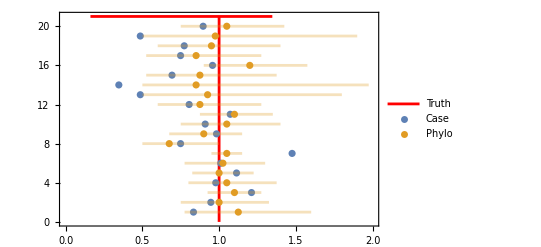

```mathematica
plot1b[4.0,20]
```

```mathematica
leg2 = LineLegend[Red,"Truth"];
```

```mathematica
plot2[λTrue_,nSim_]:=Show[DistributionChart[{Table[rEff[λTrue,intS],{intS,1,nSim}],Table[MPE[λTrue,intS][[1]],{intS,1,nSim}]},ChartStyle->{col1,col2},ChartLabels->{"Case count","Phylogeny"},FrameLabel->{{Style["",FontSize->16,Bold],None},{None,None}}],Plot[λTrue,{x,0.5,2.5},PlotStyle->Red,PlotRange->{-2,10},PlotLegends->Placed[LineLegend[{"Truth"},LabelStyle->{FontSize->10,Bold}],Scaled[{0.85,0.9}]]],LabelStyle->Directive[FontSize->14,Bold],PlotLabel->"λ: " <> IntegerString[Round[λTrue]]]
```

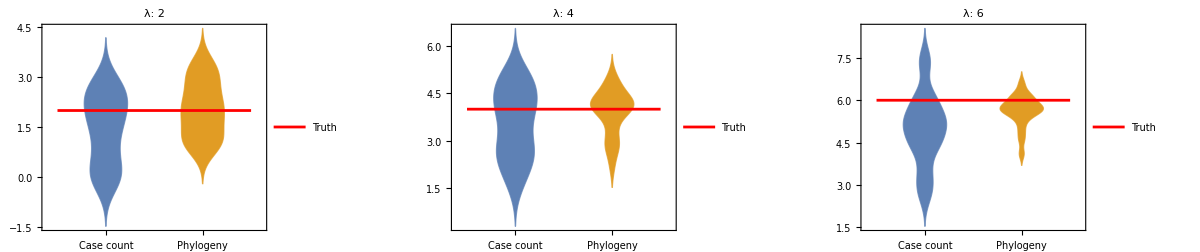

```mathematica
GraphicsRow[{plot2[2.0,20],plot2[4.0,20],plot2[6.0,20]},ImageSize->Full]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/distnYule.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/distnYule.png

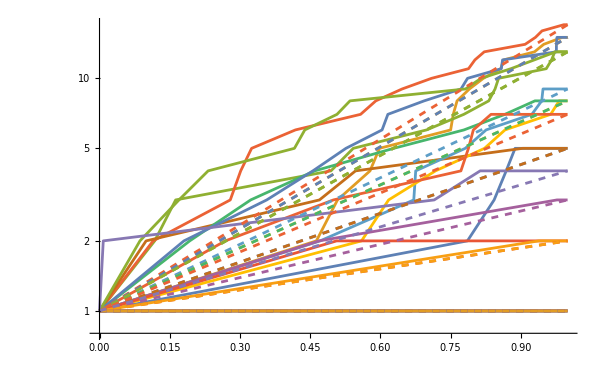

```mathematica
Show[ListLogPlot[Table[sim[2.0,intS],{intS,1,20}],Joined->True,PlotRange->All],
LogPlot[Evaluate[Table[Exp[rEff[2.0,intS]t],{intS,1,20}]],{t,0,1},PlotStyle->Dashed]]
```

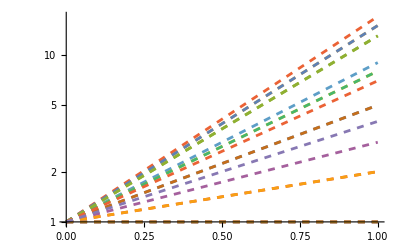

```mathematica
LogPlot[Evaluate[Table[Exp[rEff[2.0,intS]t],{intS,1,20}]],{t,0,1},PlotStyle->Dashed]
```

```mathematica
leg=PointLegend[{col1},{"Case"}];
```

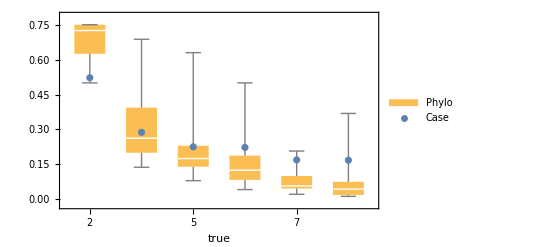

```mathematica
Show[BoxWhiskerChart[Table[Table[CILen[λ,intS]/(2λ),{intS,1,40}],{λ,{2.0,4.0,5.0,6.0,7.0,8.0}}],ChartLabels->{2,4,5,6,7,8},ChartLegends->Placed[SwatchLegend[{"Phylo"},LabelStyle->{FontSize->10}],Scaled[{0.9,0.8}]]],ListPlot[Table[StandardDeviation[Table[rEff[λ,intS],{intS,1,40}]]/λ,{λ,{2.0,4.0,5.0,6.0,7.0,8.0}}],PlotRange->All,PlotStyle->{Directive[col1]}]
,FrameLabel->{" true",""},Epilog->Inset[leg,Scaled[{0.9,0.9}]],LabelStyle->Directive[FontSize->10,Bold]]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/boxYule.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/boxYule.png